The file format for the file is a list of points with seven entries each. The entries contain the following:

1) {x, y}, the parameter values over which the loop was iterated

2) {M1, M2, M3, M0, Mtau, 
MQ, MNR, tanβ, v, vevS, 
Atop, Abtm, Atau, An11, An12,
 An13, AlambdaN, Yn11, Yn12, Yn13, 
 lambda, lambdaN, kappa, PhisPI, Phi2PI, 
 ksi, Alambda, Akappa}, the input parameters
 
3) {χN-mass(5),  χC-mass(2), H+-mass(2), ν-mass(4), snu-mass(8), 
H0-mass(6), slep-mass(6), sup-mass(2), sdn-mass(2), stp-mass(2), 
sbt-mass(2)}, the mass eigenvalues, each of these is a vector in itself with the dimension noted in parentheses.

4) {χNre(5x5), χNim(5x5), 
χC-Ure(2x2),  χCU-im(2x2), χCV-re(2x2), χCV-im(2x2),  
νre(4x4), νim(4x4), 
H0(6x6), 
snu(8x8), 
slepCre(6x6), slepCim(6x6), 
sdown-re(2x2), sdown-im(2x2), sup-re(2x2), sup-im(2x2), stop-re(2x2), stop-im(2x2), sbottom-re(2x2), sbottom-im(2x2),
H+-(2x2)}, the mixing matrices, each of these is a nxn matrix with the dimensions noted in parentheses

5) {contribution in %, absolute contribution, channel}, the contributing channels to omega

6) {omega, CDM candidate name, Xf}, self explanatory

7) {cross section in pb, input channel, output channel}, cross sections for selected channels

8) CDM nucleon magic (amp = micromegas Amplitude, cs=cross section [pb])
{{n-cdm SI amp, n-anti-cdm SI amp, n-cdm SD amp, n-anti-cdm SD amp}, 
  {p-cdm SI amp, p-anti-cdm SI amp, p-cdm SD amp, p-anti-cdm SD amp}, 
  {n-cdm SI cs, n-anti-cdm SI cs, n-cdm SD cs, n-anti-cdm SD cs}, 
  {p-cdm SI cs, p-anti-cdm SI cs, p-cdm SD cs, p-anti-cdm SD cs}}

 9) Bsgamma ect
 
 10) {{Δa_e, Δa_μ, Δa_τ},
 {d_e, d_μ, d_τ}, 
 {BR( τ -> μ γ ), BR( τ -> e γ ), BR( μ -> e γ ) }}

```mathematica
file10=<<"/Users/ruppell/Math/temp/output-cpx-higgs-phase-edm_clean3.txt";
```

```mathematica
file20=<<"/Users/ruppell/Math/temp/output-cpx-higgs-edm_clean.txt";
```

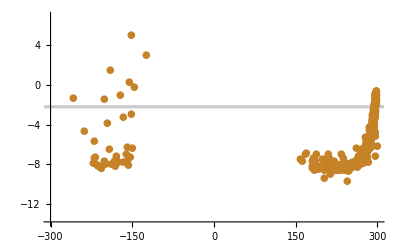

```mathematica
p2=ListLogPlot[
{Transpose@{(χ0LSP@file10)[[;;,3,1,1]],(χ0LSP@file10)[[;;,6,1]]},
Transpose@{(χ0LSP@cuts@file10)[[;;,3,1,1]],(χ0LSP@cuts@file10)[[;;,6,1]]}
},
ImageSize->400,
PlotRange->{{-300,300},{0.000001,1000}},
PlotStyle->ColorData[31,"ColorList"][[{5,9}]],
PlotMarkers->{{●,10},{●,17}},
TicksStyle->Medium,
Prolog->{Opacity[0.2,Black],Rectangle[{-500,Log@0.1311},{500,Log@0.0941}]}]
```

```mathematica
singlino component vs RD for χ0 LSP
```

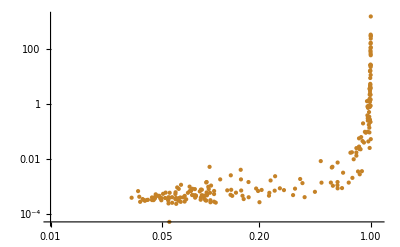

```mathematica
p2=ListLogLogPlot[
{Transpose@{Power[Abs@((χ0sing@χ0LSP@file10)[[;;,4,1]]+I(χ0sing@χ0LSP@file10)[[;;,4,2]]),2][[;;,1,5]],(χ0sing@χ0LSP@file10)[[;;,6,1]]}
},
ImageSize->400,
PlotRange->{{10^-2,1.1},{-4,3}},
PlotStyle->ColorData[31,"ColorList"][[{5}]],
TicksStyle->Medium]
```

```mathematica
κ vs RD for χ0 LSP
```

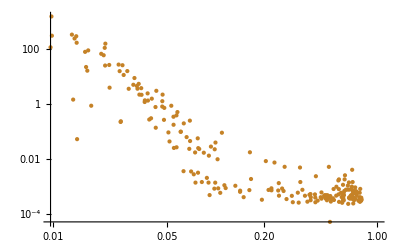

```mathematica
p2=ListLogLogPlot[
{Transpose@{Abs@(χ0sing@χ0LSP@file10)[[;;,2,23]],(χ0sing@χ0LSP@file10)[[;;,6,1]]}
},
ImageSize->400,
PlotStyle->ColorData[31,"ColorList"][[{5}]],
TicksStyle->Medium]
```

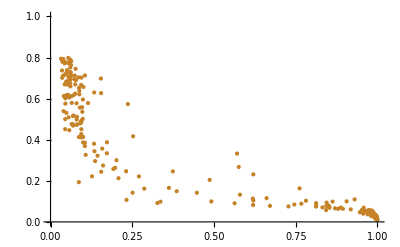

```mathematica
p2=ListPlot[
{Transpose@{Power[Abs@((χ0sing@χ0LSP@file10)[[;;,4,1]]+I(χ0sing@χ0LSP@file10)[[;;,4,2]]),2][[;;,1,5]],Abs@(χ0sing@χ0LSP@file10)[[;;,2,23]]}
},
ImageSize->400,
PlotRange->{{0,1},{0,1}},
PlotStyle->ColorData[31,"ColorList"][[{5}]],
TicksStyle->Medium]
```

```mathematica
λN vs RD for  νR LSP
```

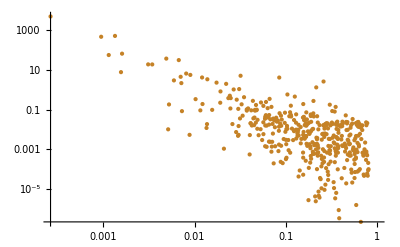

```mathematica
p2=ListLogLogPlot[
{Transpose@{(snuLSP@file10)[[;;,2,22]],(snuLSP@file10)[[;;,6,1]]}
},
ImageSize->400,
PlotStyle->ColorData[31,"ColorList"][[{5}]],
TicksStyle->Medium]
```

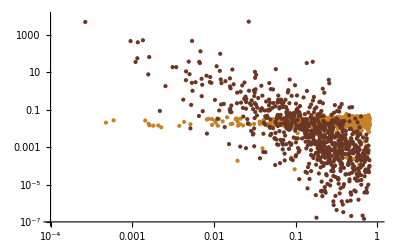

```mathematica
p2=ListLogLogPlot[
{Transpose@{(snuLeft@snuLSP@file20)[[;;,2,22]],(snuLeft@snuLSP@file20)[[;;,6,1]]},
Transpose@{(snuRight@snuLSP@file20)[[;;,2,22]],(snuRight@snuLSP@file20)[[;;,6,1]]},
Transpose@{(snuRight@snuLSP@file10)[[;;,2,22]],(snuRight@snuLSP@file10)[[;;,6,1]]}
},
ImageSize->400,
PlotRange->{{10^-4,1},{10^-7,10000}},
PlotStyle->ColorData[31,"ColorList"][[{5,3,3}]],
TicksStyle->Medium]
```

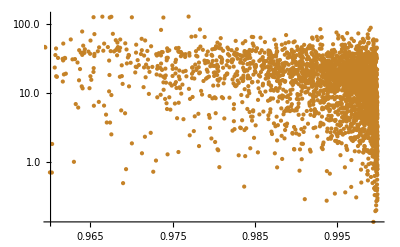

```mathematica
p2=ListLogLogPlot[
{Transpose@{Power[Abs@((file4)[[;;,4,9,2,3]]+I(file4)[[;;,4,9,2,6]]),2],(file4)[[;;,3,6,2]]}
},
ImageSize->400,
PlotStyle->ColorData[31,"ColorList"][[{5}]],
TicksStyle->Medium]
```